```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/Transition_Quantity_Generator/Mathematica_Scripts/"];
<<"Transition_Definitions.m"
ResetDirectory[];
```

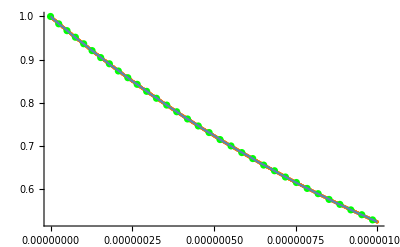

```mathematica
curdir=NotebookDirectory[]<>"tmp/";
params=Partition[BinaryReadList[curdir<>"params.bin","Real64"],5];
data=Partition[BinaryReadList[curdir<>"data.bin","Real64"],2];
data2=Partition[BinaryReadList[curdir<>"data_2.bin","Real64"],2];
Module[{Rabifreq,FWHM,Γ,tlim,sln,γ},
Rabifreq=0;
Do[Rabifreq+=(elem[[1]]+I elem[[2]]) Exp[-2 π I elem[[3]] t],{elem,params}];
FWHM=2 π params[[1]][[4]];
Γ=params[[1]][[5]];
γ=Γ+FWHM;
tlim=data[[Length[data]]][[1]];
sln=NDSolve[{pee'[t]==-I Rabifreq/2 pge[t]+Conjugate[-I Rabifreq/2 pge[t]]-Γ pee[t],pgg'[t]==I Rabifreq/2 pge[t]+Conjugate[I Rabifreq/2 pge[t]],pge'[t]==-(I Conjugate[Rabifreq])/2 (pee[t]-pgg[t])-γ/2 pge[t],pee[0]==0,pgg[0]==1,pge[0]==0},{pee,pgg,pge},{t,0,tlim}];
plts={Plot[pgg[t]/.sln,{t,0,tlim},PlotRange->Full],Plot[pee[t]/.sln,{t,0,tlim},PlotRange->Full]};
Show[ListPlot[data,PlotStyle->Orange],ListPlot[data2[[;;;;100]],PlotStyle->Green],Plot[(pee[t]+pgg[t])/.sln,{t,0,tlim},PlotRange->Full]]
]
```

```mathematica
Module[{optsfn,str,strarr,pathoptsfiles,matchfunc,k,mtch,pathfn,tmpass,mfe},
matchfunc[strs_,match_]:=Module[{pos,idx},
For[idx=1,idx≤Length[strs],idx++,
If[idx+Length[match]≤Length[strs]&&strs[[idx+Table[idx2,{idx2,0,Length[match]-1}]]]==match,Return[{strs[[idx+Length[match]]]}]];
];
Return[{}];
];
mfe[strs_,match_]:=Module[{tmp},
tmp=matchfunc[strs,match];
If[tmp=={},Return[{}];];
Return[{Read[StringToStream[tmp[[1]]],Number]}]];
optsfn=NotebookDirectory[]<>"Options_Files/Illumination_Opts_File_2.txt";
str=OpenRead[optsfn];
strarr=ReadList[str,Word];
Close[str];
pathoptsfiles={};
For[k=1,True,k++,
mtch=matchfunc[strarr,{"Laser","Path",ToString[k],"File","="}];
If[mtch=={},Break[];];
AppendTo[pathoptsfiles,NotebookDirectory[]<>mtch[[1]]];
];
stateass=<||>;
stateass["grS"]=MakeSFKet[{0,1/2,1/2,1/2,mfe[strarr,{"Ground","State","F","="}][[1]],mfe[strarr,{"Ground","State","mF","="}][[1]]}];
stateass["exS"]=MakeSFKet[{0,1/2,1/2,1/2,mfe[strarr,{"Excited","State","F","="}][[1]],mfe[strarr,{"Excited","State","mF","="}][[1]]}];
stateass["exP"]=MakePJIKet[{1,1/2,mfe[strarr,{"Excited","State","2J","="}][[1]]/2,mfe[strarr,{"Excited","State","2mJ","="}][[1]]/2,1/2,mfe[strarr,{"Excited","State","2mI","="}][[1]]/2}];
laserass=<||>;
laserass["det"]=mfe[strarr,{"Laser","Detuning","="}][[1]];
laserass["FWHM"]=mfe[strarr,{"Laser","FWHM","="}][[1]];
laserass["det_B0"]=mfe[strarr,{"Detuning","Field","="}][[1]];
pathparams={};
Do[
str=OpenRead[pathfn];
strarr=ReadList[str,Word];
Close[str];
tmpass=<||>;
tmpass["P"]=mfe[strarr,{"Power","="}][[1]];
tmpass["khat"]=Table[mfe[strarr,{"Wave","vector_"<>tmpstr,"="}][[1]],{tmpstr,{"x","y","z"}}];
tmpass["focus"]=Table[mfe[strarr,{"Focus_"<>tmpstr,"="}][[1]],{tmpstr,{"x","y","z"}}];
tmpass["waist"]=mfe[strarr,{"Beam","waist","(radius)","="}][[1]];
tmpass["pol"]=Table[mfe[strarr,{"Polarization_"<>tmpstr,"real","part","="}][[1]]+I*mfe[strarr,{"Polarization_"<>tmpstr,"imaginary","part","="}][[1]],{tmpstr,{"x","y","z"}}];
AppendTo[pathparams,tmpass];
,{pathfn,pathoptsfiles}];
]
```

```mathematica
Intensity[path_,pos_]:=(2 path["P"])/(π path["waist"]^2) Exp[-2 Norm[Cross[pos-path["focus"],Normalize[path["khat"]]]]^2/path["waist"]^2];
```

```mathematica
ElFld[vel_,Bvec_]:=Cross[vel,Bvec];
```

```mathematica
detuning1S2S[pos_,v_,BB_,Bvec_,path_]:=-(2 ((1.39927 10^-4)-(−2.67827 10^-5))*Sum[Intensity[pathloc,pos],{pathloc,pathparams}]+Norm[Cross[v,{1,1,1}]]^2 DCStarkdivEsq[stateass["exS"]]-(((ass2S[stateass["exS"]][[1]]-ass1S[stateass["grS"]][[1]])/h/.B->laserass["det_B0"])+2*laserass["det"])*(1/Sqrt[1-Norm[v/c]^2]-1)-2*laserass["det"]+((ass2S[stateass["exS"]][[2]]-ass1S[stateass["grS"]][[2]])/h-((ass2S[stateass["exS"]][[2]]-ass1S[stateass["grS"]][[2]])/h/.B->laserass["det_B0"])))/.B->BB;
```

```mathematica
decayrate1S2S[pos_,v_,BB_,Bvec_]:=((IonRatedivI*Sum[Intensity[path,pos],{path,pathparams}])+Sp2S+(Sp2SStarkdivEsqtot[stateass["exS"]]*Norm[ElFld[v,Bvec]]^2))/.B->BB
```

```mathematica
Rabifreq1S2S[pos_,v_,BB_,Bvec_,path_]:=Intensity[path,pos]*Rabi1S2SdivI[stateass["exS"],stateass["grS"]]/.B->BB;
```

```mathematica
detuningLyAlph[pos_,v_,BB_,Bvec_,path_]:=-(-(((ass2P[stateass["exP"]][[1]]-ass1S[stateass["grS"]][[1]])/h/.B->laserass["det_B0"])+laserass["det"]) ((1-((path["khat"]).v/c))/Sqrt[1-Norm[v/c]^2]-1)-laserass["det"]+((ass2P[stateass["exP"]][[2]]-ass1S[stateass["grS"]][[2]])/h-((ass2P[stateass["exP"]][[2]]-ass1S[stateass["grS"]][[2]])/h/.B->laserass["det_B0"])))/.B->BB;
```

```mathematica
decayrateLyAlph[pos_,v_,BB_,Bvec_]:=N[Sp2Ptot[stateass["exP"]]/.B->BB];
```

```mathematica
RabifreqLyAlph[pos_,v_,BB_,Bvec_,path_]:=Module[{xhat,yhat,zhat,tmpRabivec},
zhat=Normalize[Bvec];
yhat=Normalize[Cross[zhat,{1,0,0}]];
xhat=Normalize[Cross[yhat,zhat]];
tmpRabivec=RabiLyAlphdivsqrtI[stateass["exP"],stateass["grS"]]/.B->BB;
Return[({Normalize[path["pol"]].xhat,Normalize[path["pol"]].yhat,Normalize[path["pol"]].zhat}.tmpRabivec) Sqrt[Intensity[path,pos]]];
];
```

```mathematica
paramsLyAlph[pos_,v_,BB_,Bvec_]:=Module[{rettbl,tmpRabi},
rettbl={};
Do[
tmpRabi=RabifreqLyAlph[pos,v,BB,Bvec,path];
AppendTo[rettbl,{Re[tmpRabi],Im[tmpRabi],detuningLyAlph[pos,v,BB,Bvec,path],laserass["FWHM"],decayrateLyAlph[pos,v,BB,Bvec]}];
,{path,pathparams}];
Return[N[rettbl]];
];
```

```mathematica
params1S2S[pos_,v_,BB_,Bvec_]:=Module[{rettbl,tmpRabi},
rettbl={};
Do[
tmpRabi=Rabifreq1S2S[pos,v,BB,Bvec,path];
AppendTo[rettbl,{Re[tmpRabi],Im[tmpRabi],detuning1S2S[pos,v,BB,Bvec,path],2*laserass["FWHM"],decayrate1S2S[pos,v,BB,Bvec]}];
,{path,pathparams}];
Return[N[rettbl]];
];
```

```mathematica
Max[Abs[(params-params1S2S[{0,0,0},{30,-20,10},1,{1,1,1}])/(params+10^-100)]]
```

```mathematica
Max[Abs[(params-paramsLyAlph[{0,0,0},{30,-20,10},1,{1,1,1}])/(params+10^-100)]]
```